## PHAS2443 Mini-project Decision-making in Committees Hayk Khachatryan - 15013904

## 24/02/2018

```mathematica
Clear[modeler]

modeler[N_, {k_, {h0_, h1_}, e_}] := 
(* 
	Implementation of Parkinson's Law  for decision-making in committees;
	

	inputs:
;	
		N: committee size (N ∈ ℕ);

		{k, h, e}: model parameters;
			k: connectivity (number of undirected links between nodes) (k ∈ ℕ);
			h: threshold (h ∈ [0.5, 1]);
			e: rewiring probability (e ∈ [0, 1]);

	outputs:
;
		graph probs
*)

Module[
{},

]


modeler::usage = "D[N, {k, h, e}] gives the expectation value of a final state without consensus and measures the groups proneness to end up in dispute"
```

D[N, {k, h, e}] gives the expectation value of a final state without consensus and measures the groups proneness to end up in dispute

```mathematica
dissensus[n_, sf_, si_] := 
HeavisideTheta[
1-Max[sf, n-sf]/n]
```

```mathematica
dissensus[15,3,10]
```

1

```mathematica
Graph[{1 <-> 2, 2<-> 3, 2<-> 4, 1<-> 4}]
```

-Graphics-

### Need to implement the majority update func

```mathematica
Clear[majority]

majority[h_,list_]:=
(*
	Returns 1 if a majority above the threshold 'h' is reached;
	Returns 0 if no majority above the threshold 'h' is reached;

	inputs;
		h: threshold;
		list: list of elements to check
*)
Module[
{l = list  //.{1 -> True, 0 -> False}},


BooleanCountingFunction[
{
IntegerPart[h Length[list]],
Length[list]
},
Length[l]
] @@ list


]
```

Majority fails to return True for a majority of state 0. This is because BooleanCountingFunction creates a logical statement comparing the elements in the list to each other to see if they’re the same. For a list { a, b, c, d } with h = 0.75, it checks

```mathematica
( a ∧ b ∧ c) ∨ ( a ∧ b ∧ d ) ∨ ( b ∧ c ∧ d )
```

(a&&b&&c)||(a&&b&&d)||(b&&c&&d)

While this works when the majority has a state of 1, it fails to work when the majority has a state of 0 (as 0 ∧ 0 ∧ 0 = 0)

```mathematica
Simplify[( a ∧ b ∧ c) ∨ ( a ∧ b ∧ d ) ∨ ( b ∧ c ∧ d ) /. {a -> 1, b -> 1, c-> 1, d -> 0}]
Simplify[( a ∧ b ∧ c) ∨ ( a ∧ b ∧ d ) ∨ ( b ∧ c ∧ d ) /. {a -> 1, b -> 0, c-> 0, d -> 0}]
```

True

False

```mathematica
Clear[swaps]

swaps[h_, list_, 0] :=
If[majority[h,list],1,0]
swaps[h_,list_, 1] :=
If[majority[h,list], 0, 1]
swaps[h_, list_, e] :=
If[majority[h,list],1,0]
```

## 25/02/2018

Working on a majority function that takes into account  0 ∧ 0 = 0

```mathematica
Clear[majority]

majority[h_,list_]:=
(*
	Returns 1 if a majority above the threshold 'h' is reached;
	Returns 0 if no majority above the threshold 'h' is reached;

	inputs;
		h: threshold;
		list: list of elements to check
*)
Module[
{l = list  //.{1 -> True, 0 -> False}},


BooleanCountingFunction[
{
IntegerPart[h Length[list]],
Length[list]
},
Length[l]
] @@ l


]

vars = {0,0,0,0,0}
```

{0,0,0,0,0}

```mathematica
l
```

{0,0,0,0,1}

{b,2 b,3 b,4 b,5 b}

```mathematica
h = 0.6
list = {False, False, False, False, True}
l = {0,0,0,0,1}
ab = {a,b,c,d,e}

fdsa = BooleanConvert[
BooleanCountingFunction[
{
IntegerPart[h Length[list]],
Length[list]
},
Length[list]
] @@ Table[bdd i, {i, 1, Length[l]}] ] 


(* then swap the bdd's back with rules *)
```

0.6

{False,False,False,False,True}

{0,0,0,0,1}

{a,b,c,d,e}

(bdd&&2 bdd&&3 bdd)||(bdd&&2 bdd&&4 bdd)||(bdd&&2 bdd&&5 bdd)||(bdd&&3 bdd&&4 bdd)||(bdd&&3 bdd&&5 bdd)||(bdd&&4 bdd&&5 bdd)||(2 bdd&&3 bdd&&4 bdd)||(2 bdd&&3 bdd&&5 bdd)||(2 bdd&&4 bdd&&5 bdd)||(3 bdd&&4 bdd&&5 bdd)

```mathematica
majority[0.8,{0,0,0,1,0}]
```

False

(0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0)

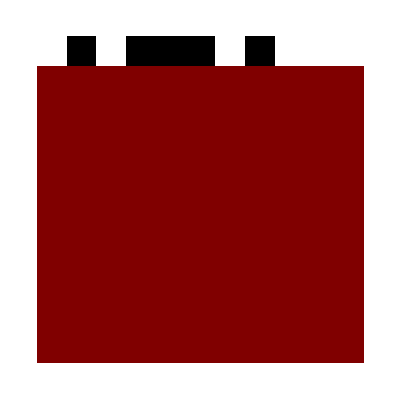

```mathematica
up[lst_,t_]:=BooleanConvert[majority[0.6,lst]]


With[
{
init={0,1,0,1,1,1,0,1,0,0,0},
nsteps=10,
r=2
},
res=CellularAutomaton[{up,{},r},init,nsteps]
];
MatrixForm[res] //. {0 -> False, 1-> True} //. {False -> 0, True -> 1}

ArrayPlot[res]
```